# (Monte-Carlo) Positron-Emission- Entanglement Tracking Simulation (MC P.E.E.T.S)

Nathan Ngqwebo

University of Cape Town

```mathematica
Clear["Global`*"];
(*Quit[];*)
```

## Cross sections

Some Constants:

```mathematica
electronRadius=2.8179403227*10^-13 ; (*electron radius in cm*)
electronMass=9.10938*10^-28; (*electron mass in grams*)
r=1; (*can do this because σKN is only used for the (dimensionless) scattering angle. Moreover, we only need the distribution*)
ρ=5.76; (*g/cm^3 CdZnTe mass density: Detector material*)
$Assumptions γ >0;
```

Klein-Nishina

From the Klein-Nishina cross-section for Compton interactions, we have the differential cross-section describing the proportion of γ-rays scattered off a small crossection dσ into a solid angle dΩ.
SHORTHAND: x = cos(θ)

```mathematica
dσdΩ[x_, γ_] = r^2/2(1+x^2+(γ^2(1-x)^2)/(1+ γ (1-x)))/(1+γ (1-x))^2;(*Almost a valid PDF. Just needs normalisation*)
```

Here, we find the area under the differential cross-section to give us our normalisation constant σ_KN.

```mathematica
σKN[γ_]= 2π Integrate[dσdΩ[x,γ],{x,-1,1},Assumptions->{γ>0, -1<=x<=1}]//FullSimplify;
```

Now, we can have a valid PDF for the scattering angle x i.e., θ.

```mathematica
pKN[x_, γ_]=(2Pi dσdΩ[x,γ])/σKN[γ] ;
(*2Pi factor from integrating out the ϕ dependence of pKN and leaving a marginal PDF in x and γ*)
```

CDF at the endpoint = 1 ?

```mathematica
Integrate[pKN[x,γ],x];
cdfKN[x_,γ_]=%-(%/.x->-1)//FullSimplify;
Manipulate[Plot[cdfKN[x, γ],{x,-1,1},AxesLabel->{"x=Cos(θ)", "CDF_KN(x)"}, Filling->Bottom, PlotStyle->Black],{{γ, 1, "E_γ/m_e"},1*10^-3,1}]
```

PDF >= 0 ?

```mathematica
Manipulate[Plot[pKN[x, γ],{x,-1,1},AxesLabel->{"x=Cos(θ)", "p_KN(x)"}, Filling->Bottom, PlotStyle->Black],{{γ, 1, "E_γ/m_e"},1*10^-3,1}]
```

Checking against the expected value of σ_KN.

```mathematica
ΣKN[γ_]=2π r^2((1+γ)/γ^2 ((2(1+γ))/(1+2 γ)-Log[1+2 γ]/γ)+Log[1+2 γ]/(2 γ)-(1+3 γ)/(1+2  γ)^2)// Simplify;
N[σKN[γ]/ΣKN[γ]] //FullSimplify
```

1.

Nice!

Experimental Data

```mathematica
(*Defining the total crossection Subscript[σ, T] from absorbtion and Compton cross sections using NIST experimental data*)
(*Be sure to have a NIST cross section data .csv in the same directory as the notebook*)
$filepath = FileNameJoin[{NotebookDirectory[], "CdZnTe_Cleaned.csv"}];
$data = Import[$filepath,"Dataset","HeaderLines"->1][All,{"photonEnergy", "photoelectricAbsorbtion", "incoherentScatter","totalNoCoherent", "totalWithCoherent"}];
$energy = $data[All, 1] //Normal;
$absorbtion = $data[All, 2]//Normal;
$compton= $data[All, 3]//Normal;
$totalcross = $data[All,4]//Normal;
$totalcrossCoh = $data[All,5]//Normal; (*we don't expect coherent scattering to have much impact on Subscript[σ, T]*)
(*Interpolating the log data is much smoother than using the raw data*)
$logσA = Interpolation[Transpose[{$energy, Log[$absorbtion]}], Method->"Hermite"];
$logσC=Interpolation[Transpose[{$energy, Log[$compton]}], Method->"Hermite"];
$logσTot  =Interpolation[Transpose[{$energy, Log[$totalcross]}], Method->"Hermite"];
$logσTotCoh  =Interpolation[Transpose[{$energy, Log[$totalcrossCoh]}], Method->"Hermite"];
(*converting back to regular crossections as pure-functions*)
σA[γ_]:=E^($logσA[γ]);
σC[γ_]:=E^($logσC[γ]);
σTot[γ_]:=E^($logσTot[γ]);
σTotCoh[γ_]:=E^($logσTotCoh[γ]);
```

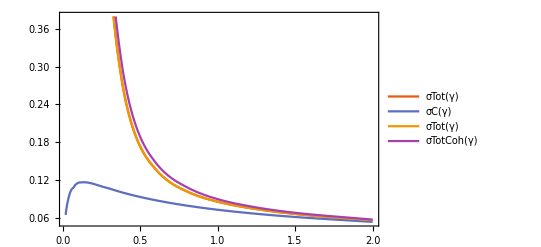

```mathematica
Plot[{σTot[γ], σC[γ], σTot[γ], σTotCoh[γ]},{γ,0.02,2}, PlotLegends->"Expressions", PlotTheme->"Scientific", GridLines->{{0.02, 1/3, 2/3,1}}]
```

## Beam Modelling

### Sampling

We need to sample a few key parameters: path length, scattering angles, scattering angle correlation, photon energy loss, etc...

```mathematica
SeedRandom[34]
```

RandomGeneratorState[…]

#### Sampling distance travelled through medium: s

```mathematica
λ[γ_]:=1/(ρ σTot[γ]) ; (*mean free path*)
pS[S_, γ_]:=1/λ[γ] E^(-S/λ[γ]) //Simplify;
cdfS[S_, γ_]:= 1 - E^(-S/λ[γ])
inverseCDFS[rs_, γ_]:= (-Log[rs])/(ρ σTot[γ]);
samplePathLength[γ_]:= (-Log[RandomReal[]])/(ρ σTot[γ]);
```

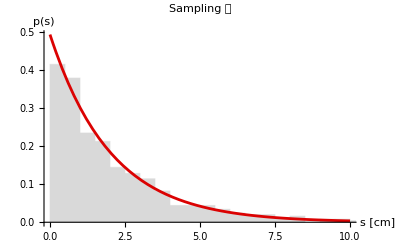

```mathematica
data=Table[samplePathLength[1], 10^3];
Show[
Histogram[data, Automatic,"PDF",PlotLabel->"Sampling 𝓈",ChartStyle->LightGray, PlotRange->{{0, 10}, All}],
Plot[pS[S, 1], {S, 0, 10}, PlotStyle->2, PlotRange->Full],
AxesLabel->{Style["s [cm]", Bold, Medium], Style["p(s)", Bold, Medium]}]
```

#### Sampling Azimuthal Scattering angle :ϕ

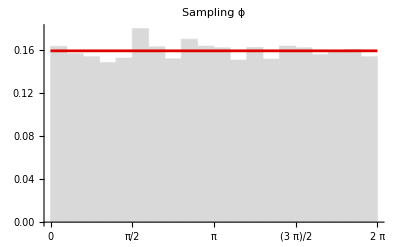

```mathematica
sampleAzimScatter[]:=2π RandomReal[]; (*easy peazy*)
rϕ= RandomReal[2π, 10^4];
Show[Histogram[rϕ,{π/10},"PDF",PlotLabel->"Sampling ϕ",ChartStyle->LightGray, Ticks->{Range[0, 2π, π/2], Automatic}], 
Plot[1/(2π), {ϕ, 0, 2π}, PlotStyle->2]]
```

#### Sampling Polar scattering angle: θ [First attempt]

We only need to sample for the cases when γ != 1. So we perform inverse cdf sampling on a 7^th-order for various γ values.

```mathematica
(*seriesCDFKN[x_, γ_]= Series[cdfKN[x, γ],  {x, 0, 8}] ;
seriesInverseCDFKNRight[y_, γ_] = InverseSeries[Series[cdfKN[x, γ],  {x, 1, 5}], y];
seriesInverseCDFKNLeft[y_, γ_] = InverseSeries[Series[cdfKN[x, γ],  {x, -1, 5}], y];*)
```

```mathematica
(*xData = Subdivide[-1., 1, 10^2];
cdfData = cdfKN[xData, 1];
points = Transpose[{cdfData, xData}];
(*Cubic Spline interpolation*)
inverseCDFKN = Interpolation[points, Method->"Spline"];
Manipulate[Show[
ListPlot[Transpose[{cdfKN[xData, γ],xData  }], PlotLabel->"Left and Right Power Series Expansions of inverseCDFKN",AxesLabel->{"r_θ = p_KN(x)", "x=Cos(θ)"}, Axes->{True,True}, PlotStyle->Black], 
Plot[{Evaluate[Normal[seriesInverseCDFKNRight[r, γ] ]], Evaluate[Normal[seriesInverseCDFKNLeft[r, γ] ]]}, {r, 0, 1}, PlotLegends->"Expressions"]], {{γ, 0.33, "E_γ/m_e"}, 11/511, 1}]
*)
```

We   may   have   trouble   with   sampling   values   of   x -> 1   because   of   resolution . 
[TODO] : I   propose   splitting   the   xData   into   Left   and   Right   for   x : cdfKN[x] < 50  %   and   x : cdfKN[x] > 50  % .
and   increasing   the   number   of   points   in   xDataRight .
This   may   make   interpolation   smoother?

```mathematica
(*Histogramming the sampled data*)
(*I think Mathematica is treating the area below x = 0 as negative, thus messing up the normalisation of the histogram.*)
(*dataθ =inverseCDFKN[RandomReal[1,10^5]];
Show[
Histogram[dataθ,{-1, 1, 0.05},"PDF",PlotLabel->"Sampling θ", PlotRange->All,ChartStyle->LightGray],
Plot[pKN[x, 1], {x,-1, 1},PlotRange->All, PlotStyle->2],
AxesLabel->{"x = Cos(θ)", "p_KN(x)"}]*)
```

I may need a 3D inverseCDF: NAH!! NO NEED!
[TODO:] xData, γData meshgrid -> cdf[xv, γv] -> Invert(x=cdf reflection?) -> InverseCDF

```mathematica
(*γData = Subdivide[0.0001, 1, 10^2];
inverseCDFData=Table[(*Calculate inverse CDF data for each gamma*)xData=Subdivide[-1.,1,10^2];
cdfData=cdfKN[xData,γ];
points=Transpose[{cdfData,xData}];
Interpolation[points,Method->"Spline"],{γ,γData}]

(*Define a function to interpolate inverse CDF based on gamma*)inverseCDFInterpolated[γ_?NumericQ]:=inverseCDFData[[Nearest[γData,γ][[1]]]][γ];
(*Sample from the interpolated inverse CDF*)
dataTheta=Table[inverseCDFInterpolated[RandomChoice[γData]][RandomReal[]],{10^5}];*)
```

#### Sampling latitudinal scattering angle: θ [credit: A.P.]

```mathematica
(*set up regular grid for the inverse cdf: Subscript[ICDF, KN]*)
$γmin=0.02;$γmax=1;
$nγ=64;$nξ=64;$nr=64;
(*generate list of 1D interpolations which are slices of the Subscript[ICDF, KN] in constant γ *)
$ξC[γ_]:=Interpolation[{cdfKN[#,γ],#}&/@ Subdivide[-1.,1,$nξ]];
$ξC[#][Subdivide[0.,1,$nr]]&/@ Subdivide[$γmin,$γmax,$nγ];
(*stitch interpolations into an Subscript[ICDF, KN] surface*)
inverseCDFKN=ListInterpolation[Transpose@%,{{0,1},{$γmin,$γmax}}];
samplePolarScatter[γ_]:=inverseCDFKN[RandomReal[], γ];
```

#### Photon Energy change after scatter

γ' = γ/(1+ γ(1-x)) (from the Compton formula)

```mathematica
δγ[γ_, x_]= (γ^2(1-x))/(1+ γ(1-x)); (*δγ = γ' -γ*)
```

#### Sampling Interaction type

```mathematica
interactionType[γ_]:=If[RandomReal[]<σC[γ]/σTot[γ], 1, 0]; (*1 - Compton & 0 - Absorption*)
```

#### Sampling detector face Hit-point & Initial Photon state

Placing an isotropically emitting source a distance z_0 away from the detector face, we will observe an incident γ-ray intensity pattern which goes as ℐ∝1/r^2. From this we can sample hit-points on the detector face.

```mathematica
(*Define a module that initializes the inverse CDF for the intenesity pattern and provides a method for sampling hit points*)
generateStateSampler[z0_,{a_,b_},{c_,d_},gridResolution_:{16,16}]:=Module[{f,𝒻,Nx,Ny,Δx,Δy,$x,$y,$𝒻,CMF,CMFindices,inverseCMF,Pair,ijPoint,X,Y},

(*Define distribution*)
(*z0 is the source-detector separation along z-axis*)
f[x_,y_]=1/(x^2+y^2+z0^2);

(*Normalise distribution*)
𝒻[x_,y_] = f[x,y] / NIntegrate[f[x,y],{x,a,b}, {y,c, d}];

(*Discretize PDF*)
Nx= gridResolution[[1]];
Ny = gridResolution[[2]];
Δx = (b-a)/Nx;
Δy = (d-c)/Ny;

(*Divide domain into Nx*Ny (centered) cells*)
$x[j_]:=a +Δx (j - 1/2);
$y[i_]:=c+Δy (i - 1/2);

(*Compute distribution values on the grid*)
$𝒻=Table[𝒻[$x[j],$y[i]], {j, 1, Nx}, {i, 1, Ny}];

(*Flatten and cumulatively sum discretized distribution into a cumulative mass function CMF*)
CMF = Prepend[Accumulate[Flatten[$𝒻]*(Δx  Δy)],0];
CMFindices = Range[0, Nx Ny];

(*Numerically invert and interpolate the CMF*)
inverseCMF = Interpolation[Transpose[{CMF, CMFindices}]];

(*helper function: Convert sampled path length to (i,j) pair*)
Pair[ℓ_]:={Quotient[ℓ-1, Ny]+1, Mod[ℓ-1,Nx]+1};

(*Get (i,j) pair from uniform r ∈ [0, 1]*)
ijPoint[r_]:=Pair[Ceiling[inverseCMF[r]]];

(*Add uniform noise to spread (Subscript[x, j],Subscript[y, i]) position over grid cell*)
X[x_]:=x+RandomReal[{-Δx/2, Δx/2 }];
Y[y_]:= y+RandomReal[{-Δy/2, Δy/2 }];

(*method to sample full photon state*)
samplePhoton[]:=Module[{r,i,j, x, y, θ, ϕ},
r=RandomReal[];
{i, j} = ijPoint[r];
x=X[$x[j]];
y=Y[$y[i]];
θ=ArcTan[z0, Sqrt[(x^2+y^2)]];
ϕ=ArcTan[x, y];
Return[
{{x, y, z0}, {θ,ϕ}, 1, 0}];
];
(*Returns the Function to sample full photon state*)
samplePhoton
]
```

#### Sampling Relative azimuthal angle Δϕ [Credit: A.P.]

```mathematica
(* PDF: double-Compton scattering of entangled γ pair [Pryce1947] *)
p[x1_,x2_,φ_]=(kA[x1]kA[x2]-kB[x1]kB[x2]Cos[2φ])/π;
kB[x_]=(1-x^2)/(2-x)^2;
(* conditional PDF: p(φ|Subscript[x, 1] Subscript[x, 2]); ϕi = Subscript[k, B][Subscript[x, 1]]Subscript[k, B][Subscript[x, 2]]/(Subscript[k, A][Subscript[x, 1]]Subscript[k, A][Subscript[x, 2]]) *)
pφ=2/π-β Cos[2φ];
(* CDF of Subscript[p, φ] for given β *)
cφ[φ_,β_]=(2φ)/π-β/2 Sin[2φ];
(* to calc random φ from uniform random r for given β
 $φ0: start point for FindRoot, from polynomial interpolation of pφ
  NB: FindRoot gives value in [0,π/2], then random sign (Symmetry savings!)
 *)
$φ0[r_,β_]=π (2β+√((1-2β)^2+8β r)-1)/(8β)//Abs;
Â©φ[r_,β_]:=RandomChoice[{-1,1}]φ/.FindRoot[cφ[φ,β]==r,{φ,$φ0[r,β]}]
sampleDeltaPhi[x1_, x2_]:=Â©φ[RandomReal[],(kB[x1]kB[x2])/(pKN[x1, 1]pKN[x2, 1])]
```

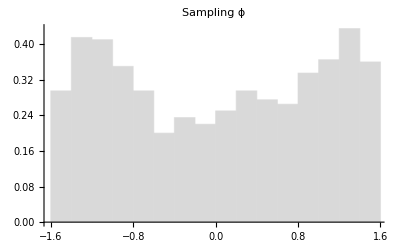

```mathematica
r©φ= Table[sampleDeltaPhi[samplePolarScatter[1], samplePolarScatter[1]], 10^3];
Show[Histogram[r©φ,Automatic,"PDF",PlotRange->{{-1.02π/2, π/2}, Automatic},PlotLabel->"Sampling ϕ",ChartStyle->LightGray ], Ticks->{Range[-2π, 2π, π/4]}]
```

## Simulation

## Detector Dimensions

```mathematica
(*Detector geometry and resolution parameters (see sketch)*)
a = 10; b=10; c=14; z0=6;
energyResolution = 0.02; (*energy threshold for detectable photons*)

(*Cuboid region test fenerator based on 6 plane position test*)
generateDetectorRegion[{{xlower_, xupper_}, {ylower_, yupper_}, {zlower_, zupper_}}]:=Module[{isInDetector},
isInDetector[{x_, y_, z_}]:=If[xlower <=x <= xupper && ylower <=y <= yupper && zlower <=z <= zupper, Return[True], Return[False]];
Return[isInDetector]
]

(*Energy resolution test generator*)
generateEnergyResolutionLimit[γmin_]:=Module[{isγResolved},
isγResolved[γ_]:=If[γ >= γmin,Return[True], Return[False]];
Return[isγResolved]
]
```

```mathematica
(*Initialize detector region and resolution tests*)
withinDetector1 = generateDetectorRegion[{{-a,a}/2,{-b,b}/2, {0, c+z0}}];
withinDetector2 = generateDetectorRegion[{{-a,a}/2,{-b,b}/2, {-z0-c, -z0}}];
isEnergyResolved = generateEnergyResolutionLimit[energyResolution];

(*Initialise photon state sampler [need only sample for Detector1 because Detector2's photon is an inversion]*)
samplePhotonD1= generateStateSampler[z0, {-a, a}/2,{-b,b}/2, {16,16}];
```

## mETHODS

Particles are implemented as a State variable with:
	position{𝓍, 𝓎, 𝓏}, 
	direction{θ, ϕ} (unit vector of momentum),  
	energy{γ}, 
	Δenergy [Δγ] (for convenience)

```mathematica
(*spherical polar to cartesian function*)
fromSphericalCoords[r_, {θ_, ϕ_}]:={
r Sin[θ] Cos[ϕ], 
r Sin[θ] Sin[ϕ],
r Cos[θ]
};
```

```mathematica
(*From the inner product of spherical polar unit vectors r̂(Subscript[θ, 1], Subscript[ϕ, 1]) and r̂(Subscript[θ, 2], Subscript[ϕ, 2])*)
updatedDirection[{θi_, ϕi_}, Θ_,  Φ_]:=Module[{θ1=θi, ϕ1=ϕi, θ2, ϕ2, Δϕ, cosΔϕ1, sinΔϕ2},
θ2=ArcCos[Cos[θ1] Cos[Θ]+Sin[θ1] Sin[Θ] Cos[Φ]];
cosΔϕ1=(Cos[Θ] - Cos[θ2] Cos[θ1])/(Sin[θ1] Sin[θ2]);
sinΔϕ2=(Sin[Θ] Sin[Φ])/Sin[θ2];
(*Δϕ=ArcTan[sinΔϕ2/cosΔϕ1]; (*Does not respect sign -> quadrant of origin!!*) *)
Δϕ=ArcTan[cosΔϕ1, sinΔϕ2]; (*Thanks, David*)

{ θ2, Δϕ+ϕ1}
];
```

```mathematica
(*Compton interaction process*)
comptonScatter[{{x0_, y0_, z0_}, {θ0_, ϕ0_},γ0_ , dγ_}]:=Module[{Φ, 𝕩, Δγ, γ=γ0, direction}, 
(* Sample uniform azimuthal scattering angle*)
Φ=sampleAzimScatter[]; 
(* Sample polar scattering angle from Subscript[dσ, KN] dΩ*)
𝕩=samplePolarScatter[γ0] ;
(*Update energy post-scatter*)
Δγ=δγ[γ0, 𝕩]; 
(* decrement photon energy according to Compton formula*)
γ-= Δγ;
direction=updatedDirection[{θ0, ϕ0},  ArcCos[𝕩], Φ];
Return[{{x0, y0, z0},direction,γ, Δγ}]
]

(*Double Compton interaction process*)
doubleComptonScatter[photon1_, photon2_]:=Module[{x1, x2, Δγ1, Δγ2, Δφ, φ1, φ2, P1 = photon1, P2=photon2},
(*sample polar scattering angles*)
{x1, x2} = {samplePolarScatter[P1[[3]]],samplePolarScatter[P2[[3]]]};

(*update energies post-scattering*)
Δγ1=δγ[P1[[3]], x1]; 
Δγ2=δγ[P2[[3]], x2]; 
P1[[4]]=Δγ1;
P1[[3]] -=Δγ1;
P2[[4]]=Δγ2;
P2[[3]] -=Δγ2;

(*sample relative azimuthal angle*)
Δφ =sampleDeltaPhi[x1, x2];

(* sample uniform azimuthal scattering angle: P1*)
φ1 =sampleAzimScatter[];
(* calculate φ2 azimuthal scattering angle via Δφ: P1*)
(*φ2 = sampleAzimScatter[];*) (*UNCOMMENT for zero entanglement*)
φ2 =φ1-Δφ;

(*update directions*)
P1[[2]] = updatedDirection[P1[[2]], ArcCos[x1],φ1];
P2[[2]] = updatedDirection[P2[[2]], ArcCos[x2],-φ2];
{P1, P2}
]

(*Generate a photon on D1 and its reflection on D2*)
samplePhotonPair[] :=Module[{P1, P2},
(*sample photon1 state on Detector1 and reflect to produce photon2*)
(*P1 = samplePhotonD1[];*) (*UNCOMMENT for isotropic source*)
P1={{0, 0, z0},{0.0001, 0.0001}, 1,0}; (*UNCOMMENT for photon beams*)
(*Reflect photon onto Detector-2 face*)
P2 = {-P1[[1]], P1[[2]] + {π,0}, 1, 0};
{P1, P2}
]

(*Sampling entangled photons who's initial interaction is a compton scatter*)
seedDoubleComptonPhotons[]:=Module[{count, P1, P2,newP1,newP2, s1, s2, protoHistoryP1, protoHistoryP2},
count=0;

(*A double scattering event is so likely, we hardly ever get past 5 iterations (in a large enough detector system)*)
While[count < 101,
count++;

(*sample photon1 state on Detector1 and reflect to produce photon2*)
P1 = samplePhotonD1[]; (*UNCOMMENT for isotropic source*)
(*P1={{0, 0, z0},{0.0001, 0.0001}, 1,0};*) (*UNCOMMENT for photon beams*)
P2 = {-P1[[1]], P1[[2]] + {π,0}, 1, 0};

(*sample path length given initial 511 keV energy*)
s1 =samplePathLength[1];
s2 =samplePathLength[1];

(*update photon positions*)
P1[[1]]+=fromSphericalCoords[s1,P1[[2]]];
P2[[1]]+=fromSphericalCoords[s2,P2[[2]]];

(*Check for either photon's escape OR absorption*)
If[withinDetector1[P1[[1]]] && withinDetector2[P2[[1]]] && (interactionType[1] !=0),
(*condition met: Compton pair interactions within detectors*)
{newP1, newP2} = doubleComptonScatter[P1, P2];
Return[{newP1, newP2}]
,
(*condition unmet: try again*)
Continue[]
];
];
Print["Double-Compton seeding exceeded 101 attempts..."]
]
```

```mathematica
(*Function to generate a photon's propagation history given a photon object and a detector boundary checker*)
propagatePhoton[photon_, withinDetector_]:=Module[{absorbed,escaped,interaction},
absorbed=False;
escaped=False;
NestWhileList[Module[{newPhoton=#},
(*Record initial photon state & subsequent updated states*)
s = samplePathLength[newPhoton[[3]]];
newPhoton[[1]] += fromSphericalCoords[s, newPhoton[[2]]];
If[!withinDetector[newPhoton[[1]]],
escaped=True;
newPhoton[[4]]=0;
newPhoton,
(*Switch-Case for different interaction types*)
interaction=interactionType[newPhoton[[3]]];
Switch[interaction,
0,
(
absorbed=True;
(*Store absorbed energy*)
newPhoton[[4]]=newPhoton[[3]];
(*Set energy to 0*)
newPhoton[[3]]=0;
newPhoton  
),
1,
(
(*Compton scatter*)
newPhoton=comptonScatter[newPhoton];
newPhoton
),
_,
(*Default case*)
(
newPhoton
)
]
]
]&,
photon, isEnergyResolved[#[[3]]] && !absorbed &&!escaped&, 1, 27]
]
```

## Sim (Single Detector)

```mathematica
simulatePhotons[numPhotons_]:=Module[{photons,histories},
photons=Table[samplePhotonD1[],{numPhotons / 2}];(*Half Cycles for Similar performance after adding photon pairs*)
histories=propagatePhoton[#, withinDetector1]&/@photons;
histories
]

(*Example usage*)
numPhotons=1000;
histories=simulatePhotons[numPhotons];
paths = histories[[All,All,1]];
```

### Plots

```mathematica
(*Define the detector face*)
detector1=Graphics3D[{Opacity[0.2],Gray,Cuboid[{-a/2,-b/2,z0},{a/2,b/2,c+z0}]}];

(*Define the Source*)
source = Graphics3D[{Opacity[1],Hue[0.21,0.92,1.],Cylinder[{{0,0,-1}/8,{0,0,1}/8}, 0.5]}];

(*Define the photon paths*)
photonPathsD1=Graphics3D[{Black,Table[Line[path],{path,paths}]}];

(*Combine the cuboid and the photon paths*)
scene = Show[source,detector1,photonPathsD1,Boxed->True,Axes->True, AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
(*Flattened list of photon positions of all histories and all states in each history*)
vertices = Flatten[histories[[All,All,1]],1];
(*List of cumulative δγ for each photon history *)
energyDeposits = Total[#]&/@ histories[[All,All,4]];
(*All final states with positions outside the detector *)
escaped =Select[histories[[All,All]], !withinDetector1[#[[-1, 1]]]&];
```

```mathematica
ListPointPlot3D[vertices, PlotRange->{{-a, a}/2, {-b, b}/2, {0, c+z0}},AxesOrigin->{0,0, -0.5}, AxesLabel->{"X", "Y", "Z"}, PlotStyle->{Opacity[0.3],Black, PointSize[0.01]}]
```

-Graphics3D-

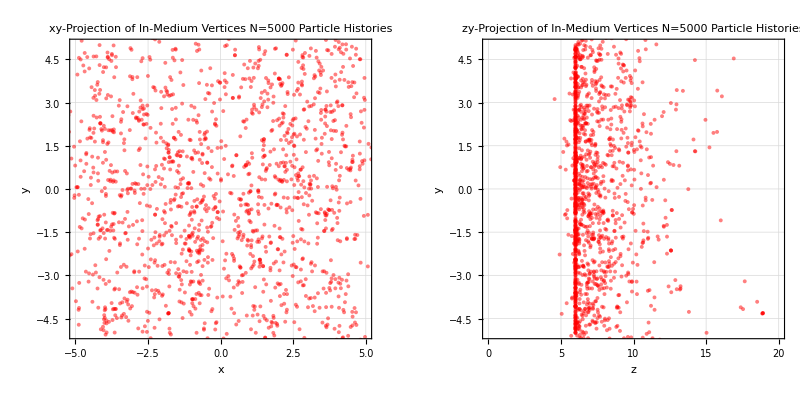

```mathematica
p1 = ListPlot[#[[1;;2]]&/@vertices, PlotRange->{{-a, a}/2, {-b, b}/2}, AxesLabel->{"x", "y"}, PlotStyle->{Red, Opacity[0.5], PointSize[0.007]}, Frame->True, AspectRatio->1, GridLines->Automatic, PlotLabel->"xy-Projection of In-Medium Vertices\n N=5000 Particle Histories",LabelStyle->Directive[Bold,Black], 
ImageSize->Full];
p2 = ListPlot[{#[[3]], #[[2]]}&/@vertices, PlotRange->{{0, c+z0}, {-b, b}/2}, AxesLabel->{"z", "y"}, PlotStyle->{Red, Opacity[0.5], PointSize[0.007]}, Frame->True, AspectRatio->1, GridLines->Automatic, PlotLabel->"zy-Projection of In-Medium Vertices\n N=5000 Particle Histories",LabelStyle->Directive[Bold,Black],
ImageSize->Full];
GraphicsRow[{p1, p2}, Background->LightBlue, Frame->True]
```

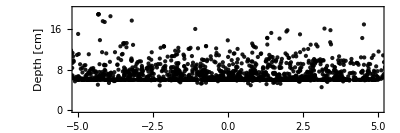

```mathematica
Graphics[{
Opacity[0.9],PointSize[Small],Point[#[[2;;3]]& /@vertices]},
Axes->{True, True},
AxesLabel->{"Distance [cm]", "Depth [cm]"},
AxesStyle->Dashed,
AxesOrigin->{0,0},
PlotRange->{{-b,b}/2,{0, c+z0}},
PlotRangeClipping->True,
Frame->True,
AspectRatio->1/3]
```

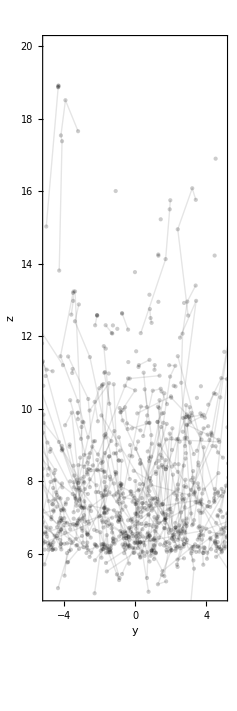

```mathematica
Graphics[{
Table[{
Opacity[0.1],Line[#[[2;;3]]&/@particleHistory[[2;;,1]]](*,Hue[RandomReal[]]*),
Opacity[0.2],Point[#[[2;;3]]&/@particleHistory[[2;;,1]]]},
{particleHistory,histories}]},
Axes->True,
AxesStyle->Dashed,
AxesLabel->{"y","z"},
AxesOrigin->{0,0},
PlotRangeClipping->True,
PlotRange->{{-b, b}/2,{c-z0*1.5,c+z0}},
Frame->True,
AspectRatio->3]
```

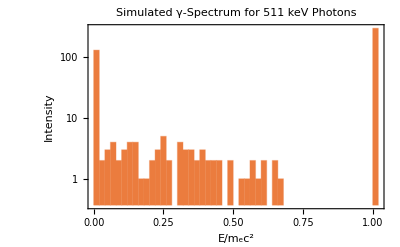

```mathematica
(*Gamma spectrum*)
Histogram[energyDeposits, {0.02}, 
Frame->True,
PlotLabel->"Simulated γ-Spectrum for 511 keV Photons",
FrameLabel->{"E/m_ec^2", "Intensity"},
ScalingFunctions->"Log",(* PlotRange->{{0, 1}, {0,10}}*)
PlotTheme->"Scientific",
GridLines->{{1/3, 2/3}, Automatic}]
```

## Sim (Double Detector)

```mathematica
simulatePairPhotons[numPairs_]:=Module[{comptonPairs, pairHistories}, 
comptonPairs = Table[seedDoubleComptonPhotons[], {numPairs}];
(*idiomatic mapping of the propagatePhoton function over photon pairs*)
d1PairHistories=propagatePhoton[#, withinDetector1]&/@comptonPairs[[All, 1]];
d2PairHistories=propagatePhoton[#, withinDetector2]&/@comptonPairs[[All, 2]];
Transpose[{d1PairHistories, d2PairHistories}]
]

(*Example usage*)
numPairs = 1000;
pairHistories = simulatePairPhotons[numPairs];
```

### Plots

```mathematica
(*Define the detector regions*)
detector2=Graphics3D[{Opacity[0.2],Gray,Cuboid[{-a/2,-b/2,-z0},{a/2,b/2,-z0-c}]}];

(*Define z-axis arrow*)
$Zarrow = Graphics3D[{Opacity[0.7], Hue[0.5,0.5,0], Arrow[{{0, 0, -z0-c-c/2}, {0, 0, z0+c+c/2}}]}];

(*Get photon paths in each detector*)
d1Paths = pairHistories[[All, 1, All, 1]];
d2Paths = pairHistories[[All, 2, All, 1]];

(*Helper function for path animations*)
photonPaths[s_]:=Graphics3D[{
Blue,Opacity[0.5],Table[Line[path],{path,d1Paths[[1;;s]]}],
Red,Opacity[0.5],Table[Line[path],{path,d2Paths[[1;;s]]}]
}]

(*model of double detector system*)
Manipulate[
Show[
photonPaths[s],
source, 
detector1,
detector2,
$Zarrow,
Axes->True,
AxesLabel->{"X", "Y", "Z"},
ViewPoint->Left,
ViewVertical -> {0, 1, 0},
PlotRange->{{-8, 8}, {-8, 8}, {-20, 20}},
ImageSize->400
],
{{s,1, "No. of Events"}, 1, numPairs, 1, Appearance->"Labelled"}
]
```

```mathematica
Show[
photonPaths[numPairs],
source, 
detector1,
detector2,
$Zarrow,
Axes->True,
AxesLabel->{"X", "Y", "Z"},
ViewPoint->Left,
ViewVertical -> {0, 1, 0},
PlotRange->{{-8, 8}, {-8, 8}, {-20, 20}},
ImageSize->800
]
```

-Graphics3D-

### Analysis

```mathematica
(*extract first two (always guanranteed if using seedDoubleCompton) vertices in each detector*)
planePoints = pairHistories[[All, 1;;2, 1;;2, 1]];

(*isolate pairs of in-medium points B and C in each detector*)
D1PointPairs =planePoints[[All, 1]];

D2PointPairs= planePoints[[All, 2]];

(*calculate plane normal vectors Subscript[n, 1] and Subscript[n, 2]*)
(*helper functions*)
crossProduct[pair_]:=Cross[pair[[1]], pair[[2]]]
dotProduct[pair_]:=Dot[pair[[1]], pair[[2]]]
$n1 = crossProduct /@ D1PointPairs;
$n2 = crossProduct /@ D2PointPairs;

(*calculate dot products between corresponding normal vectors*)
cosθ = MapThread[(Dot[#1, #2] / (Norm[#1] Norm[#2]))&, {$n1, $n2}];
G = MapThread[(VectorAngle[#1, #2] *RandomChoice[{-1,1}])&, {$n1, $n2}];
```

#### Plotting correlation modulation

```mathematica
Ka[x1_, x2_]=4π dσdΩ[x1,1] dσdΩ[x2,1] ;
Kb[x1_, x2_]=((1-x1^2) (1-x2^2))/((2-x1)^2(2-x2)^2);
ψ[ΔΦ_, x1_, x2_]=𝒩/(4 σKN[1])(Ka[x1, x2] - Kb[x1, x2] Cos[2ΔΦ]);
Ψ[ΔΦ_, x1_, x2_] = ψ[ΔΦ, x1, x2] /. Solve[Integrate[ψ[ΔΦ, x1, x2], {ΔΦ,0, π},{x1,-1, 1},{x2, -1, 1}]==1, 𝒩][[1]];
```

```mathematica
DirectSamples = Table[sampleDeltaPhi[samplePolarScatter[1], samplePolarScatter[1]], 10^3];
```

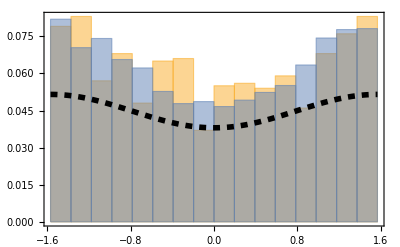

```mathematica
BinWidth={π/16};
p1 = Plot[Ψ[ΔΦ, 0.2,0.2], {ΔΦ, -π/2, π/2}, PlotStyle->{Directive, Black, Thickness[0.01], Dashed}];
h2 = Histogram[{DirectSamples,G}, BinWidth, "Probability", PlotRange->{{-π/2, π/2}, All}];
Show[{h2,p1}, Frame->True]
```